# LEPS Potential for Triatomic Reaction

## Part A

```mathematica
Clear[Vleps,qAB,qBC,qAC,jAB,jBC,jAC]
dAB=4.746 ;            (* the well depth in eV of the AB interaction *)
dBC=4.746 ;            (*      -                      BC      -      *)
dAC=3.445 ;            (*      -                      AC      -      *)
r0AB=0.742 ;         (* the bond distance in Angstrom for the AB dimer *)
r0BC=0.742 ;         (*            -                          BC   -   *)
r0AC=0.742 ;          (*            -                          AC   -   *)
alphaAB=1.942 ;   (* the exponential decay length of AB interaction *)
alphaBC=1.942 ;  (*         -                       BC      -      *)
alphaAC=1.942 ;  (*         -                       AC      -      *)
ap1=1.05 ;               (* This is written as (1+a) in the lecture notes *)
bp1=1.30 ;               (*        -           (1+b)          -           *) 
cp1=1.05;                (*        -           (1+c)          -           *)

qAB[r_] =  dAB/4 (3 Exp[-2 alphaAB (r-r0AB)] - 2 Exp[- alphaAB (r-r0AB)]);
qBC[r_] =  dBC/4 (3 Exp[-2 alphaBC (r-r0BC)] - 2 Exp[- alphaBC (r-r0BC)]);
qAC[r_] =  dAC/4 (3 Exp[-2 alphaAC (r-r0AC)] - 2 Exp[- alphaAC (r-r0AC)]);

jAB[r_] =  dAB/4 (Exp[-2 alphaAB (r-r0AB)] - 6 Exp[- alphaAB (r-r0AB)]);
jBC[r_] =  dBC/4 (Exp[-2 alphaBC (r-r0BC)] - 6 Exp[- alphaBC (r-r0BC)]);
jAC[r_] =  dAC/4 (Exp[-2 alphaAC (r-r0AC)] - 6 Exp[- alphaAC (r-r0AC)]);

Vleps[r1_,r2_] =  qAB[r1]/ap1 + qBC[r2]/bp1 + qAC[r1+r2]/cp1 -
                   Sqrt[(jAB[r1]/ap1)^2 + (jBC[r2]/bp1)^2 + (jAC[r1+r2]/cp1)^2 -
                         jAB[r1] jBC[r2]/(ap1 bp1) - jBC[r2] jAC[r1+r2]/(bp1 cp1)-
                         jAB[r1] jAC[r1+r2] /(ap1 cp1)] ;
Vleps[r1,r2]
```

1.13 (3 ⅇ^(-3.884 (-0.742+r1))-2 ⅇ^(-1.942 (-0.742+r1)))+0.912692 (3 ⅇ^(-3.884 (-0.742+r2))-2 ⅇ^(-1.942 (-0.742+r2)))+0.820238 (3 ⅇ^(-3.884 (-0.742+r1+r2))-2 ⅇ^(-1.942 (-0.742+r1+r2)))-√(1.2769 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1)))^2-1.03134 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1))) (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2)))+0.833007 (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2)))^2-0.926869 (ⅇ^(-3.884 (-0.742+r1))-6 ⅇ^(-1.942 (-0.742+r1))) (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))-0.748625 (ⅇ^(-3.884 (-0.742+r2))-6 ⅇ^(-1.942 (-0.742+r2))) (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))+0.672791 (ⅇ^(-3.884 (-0.742+r1+r2))-6 ⅇ^(-1.942 (-0.742+r1+r2)))^2)

Note that r1 and r2 in the Vleps (leps potential equation) are rAB and rBC, respectively.

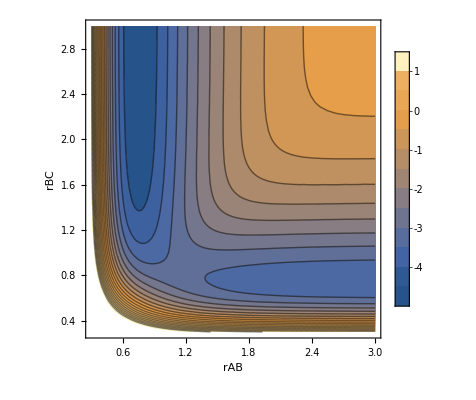

```mathematica
rMin=0.3;
rMax=3.0;
ContourPlot[Vleps[r1,r2],{r1,rMin,rMax},{r2,rMin,rMax},Contours->20,PlotLegends->{-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-.5,0,.5,1.0},FrameLabel->{"rAB","rBC"}]
```

The difference between the LEPS potential surface and the L-J potential surface is that the bottom right portion of the graph is no longer the region of minimized potential. In this LEPS plot, there are two bands - one vertical and one horizontal - where the potential is minimized instead. The bottom corner region now contains a saddle point, which represents the potential that must be overcome by the particles for the reaction to proceed to the top vertical region.

```mathematica
(*Vleps[r1,r2]/.{r1->(xb-xa),r2->(xc-xb)}*)
```

```mathematica
(*Vector gradient function with <fa, fb, fc> which are forces with respect to xa,xb,xc where r1=rab=xb-xa, r2=rbc=xc-xb*)

(*gradientForce=Grad[Vleps[r1,r2],{xa,xb,xc}]*)
```

## Part B and C

```mathematica
time=100;
h=0.02;
m=1;

xA0=-3.0;
xB0=0;
xC0=0.8;
vA0=1.0;
vB0=0;
vC0=0;

fA[r1_,r2_]=D[Vleps[r1,r2],r1];
fB[r1_,r2_]=-D[Vleps[r1,r2],r1]+D[Vleps[r1,r2],r2];
fC[r1_,r2_]=-D[Vleps[r1,r2],r2];
```

```mathematica
defV[time_,h_,xA0_,xB0_,xC0_,vA0_,vB0_,vC0_]:=(
xA[0]=xA0;
xB[0]=xB0;
xC[0]=xC0;
fa[0]=fA[xB[0]-xA[0],xC[0]-xB[0]];
fb[0]=fB[xB[0]-xA[0],xC[0]-xB[0]];
fc[0]=fC[xB[0]-xA[0],xC[0]-xB[0]];
nSteps=Round[time/h];
vA[0]=vA0;
vB[0]=vB0;
vC[0]=vC0;

For[n=0,n<=nSteps,n++,
xA[n+1]=xA[n]+vA[n]h+1/2 fa[n]/m h^2;
xB[n+1]=xB[n]+vB[n]h+1/2 fb[n]/m h^2;
xC[n+1]=xC[n]+vC[n]h+1/2 fc[n]/m h^2;
fa[n+1]=fA[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]];
fb[n+1]=fB[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]];
fc[n+1]=fC[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]];
vA[n+1]=vA[n]+1/2(fa[n]+fa[n+1])h/m;
vB[n+1]=vB[n]+1/2(fb[n]+fb[n+1])h/m;
vC[n+1]=vC[n]+1/2(fc[n]+fc[n+1])h/m;
]
)
```

```mathematica
defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]
```

```mathematica
xA[20]
vA[20]
fa[20]
```

-2.60326

0.981564

-0.0644525

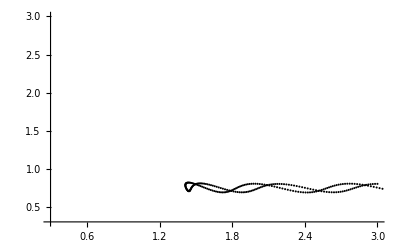

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

We see that the energy was not enough for the particles to overcome the saddle point. Instead they are stuck in the initial horizontal region where potential is minimized.

```mathematica
trajData
```

{{3.,0.8},{2.98028,0.799456},{2.96112,0.797832},{2.94251,0.795154},{2.92443,0.791462},{2.90684,0.786818},{2.88972,0.781297},4987,{99.9942,0.766395},{100.019,0.758395},{100.043,0.750051},{100.068,0.741534},{100.092,0.733027},{100.117,0.724723},{100.141,0.716819}}
 |  |  |  |

```mathematica
animationPtB=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

## Part D

```mathematica
xA0=-3.0;
xB0=0;
xC0=0.8;
vA0=1.5;
vB0=0;
vC0=0;
defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]
```

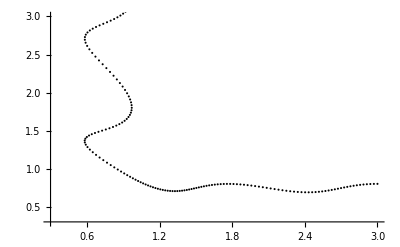

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

```mathematica
animationPtD1=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

Now we wish to return to vA0 = 1.0 and rather than adding translational energy which we just did by increasing vA0, we want to increase the vibrational energy of the BC molecule by the same amount. For this, we need to consider the equation for total energy to be the sum of the LEPS potential and the kinetic energy (1/2)mv^2. Note that the kinetic energy term only has the vA0 velocity and ignores the other particles because A is the only particle with an initial velocity. So the equation below technically represents the total initial energy, but it is also the total energy of the system through time if we assume that energy is conserved in the system. In the Vleps function, xB0-xA0 was plugged in for r1 and xC0-xB0 for r2.

```mathematica
xA0=-3.0;
xB0=0;
xC0=0.8;
vA0=1.0;
vB0=0;
vC0=0;
totalEnergy1 = Vleps[xB0-xA0,xC0-xB0]+0.5*m*1^2 (*total energy before we changed initial velocity to 1.5*)
```

-3.09311

```mathematica
totalEnergy2 = Vleps[xB0-xA0,xC0-xB0]+0.5*m*1.5^2 (*total energy after we increased initial velocity*)
```

-2.46811

The above two energies are the total energy of the system when initial velocity was 1.0 and 1.5, respectively. We want to change the potential energy while using vA0=1.0 to match the second total energy above which corresponded to energy when vA0=1.5. To do this, we can write a third energy equation as shown below. Multiple numbers were plugged in for the r2 distance using trial and error to see what distance gives the same result as totalEnergy2.

```mathematica
totalEnergy3=Vleps[3,0.558988]+0.5*m*1^2
```

-2.46811

```mathematica
vA0=1.0;
xC0=0.558988;
defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]
```

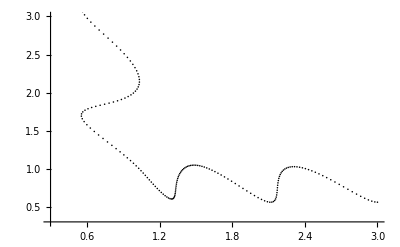

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

```mathematica
animationPtD2=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

It looks like the reaction probability is increased when potential (vibrational) energy is increased rather than kinetic (translational) energy by the same amount. This can be seen in the bottom left part of the graph where the line is almost straight as it crosses the saddle point with ease compared to the previous run with increased translational energy where a reaction still occurred but the graph went around the bottom left region less quickly.

## Part E

```mathematica
(*
old;

xA0=-3.0;
xB0=0;
xC0=0.8;
vA0=1.0;
vB0=0;
vC0=0;
*)
```

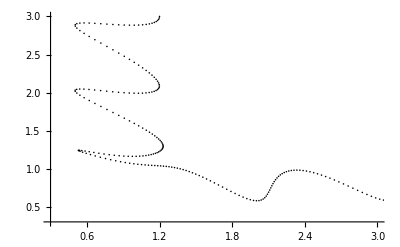

```mathematica
xA0=-1.2;
xB0=0;
xC0=3.0;
vA0=0;
vB0=0;
vC0=-1.0;

defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]

trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

```mathematica
animationPtE1=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

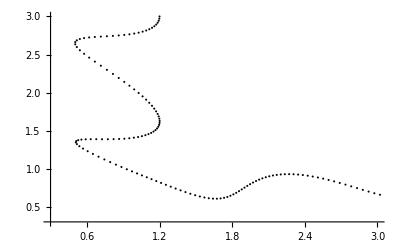

```mathematica
xA0=-1.2;
vC0=-1.5;

defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]

trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

```mathematica
animationPtE2=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

```mathematica
totalEnergy1 = Vleps[xB0-xA0,xC0-xB0]+0.5*m*1.2^2 
totalEnergy2 = Vleps[xB0-xA0,xC0-xB0]+0.5*m*1.5^2
```

-2.21916

-1.81416

```mathematica
totalEnergy3=Vleps[1.298805,3]+0.5*m*1.2^2
```

-1.81416

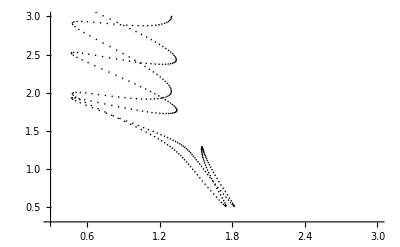

```mathematica
xA0=-1.298805;
vC0=-1;

defV[time,h,xA0,xB0,xC0,vA0,vB0,vC0]

trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]
```

```mathematica
animationPtE3=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

For this Part E reaction, the initial position had to be tweaked for particle A to a different value as the standard distance. By using the same B-C initial bond distance for the A-C bond in this scenario, I was not able to get a reaction to take place even after increasing the energy (for both a translational increase and a vibrational increase). So I changed the A-B bond distance to 1.2 as the initial standard, but kept the same initial speed of particle C as the initial speed of particle A in the previous parts. Then I increased the translational energy (increased initial velocity of C to -1.5 from -1) and the vibrational energy (reducing the A-B distance by an amount such that the total energy is the same as the total energy when translational energy was increased). After doing so, it seems that the increase in vibrational energy did not lead to a successful reaction, whereas the increase in translational energy led to an increased probability of reaction relative to the initial run where vC0= -1. This will probably vary given different reactions and conditions, but an increase in translational energy was more effective at increasing reaction probability than increasing vibrational energy was, specifically for the initial conditions that I chose.